```mathematica
Sin[x]
```

```mathematica
y1=x1^2+(2*x2+2*x3+2)*x1+2*x2^2+2*x2+2*x3^2+2*x3;
y2=2*x1-2*x3-2*x1*x2-2*x2*x3+3*x1^2+x3^2;
y3=x1^2+x2^2+x3^2;
```

```mathematica
y1
```

```mathematica
S=Solve[y1==Y1&&y2==Y2&&y3==Y3,{x1,x2,x3}]
```

```mathematica
Qu=32 Y1^2+8 Y1^3+5 Y1^4+64 Y1 Y2+32 Y1^2 Y2+64 Y2^2-128 Y3-160 Y1 Y3-104 Y1^2 Y3-40 Y1^3 Y3-320 Y2 Y3-128 Y1 Y2 Y3+336 Y3^2+320 Y1 Y3^2+120 Y1^2 Y3^2+128 Y2 Y3^2-288 Y3^3-160 Y1 Y3^3+80 Y3^4+(-256 Y1-48 Y1^2-8 Y1^3-384 Y2+128 Y1 Y2+64 Y1^2 Y2+256 Y2^2+704 Y3+160 Y1 Y3-64 Y1^2 Y3-1024 Y2 Y3-256 Y1 Y2 Y3+448 Y3^2+352 Y1 Y3^2+256 Y2 Y3^2-384 Y3^3) z+(768-512 Y1-152 Y1^2+44 Y1^3-1536 Y2+192 Y1 Y2+32 Y1^2 Y2+384 Y2^2+3232 Y3+368 Y1 Y3-320 Y1^2 Y3-1536 Y2 Y3-128 Y1 Y2 Y3+736 Y3^2+752 Y1 Y3^2+128 Y2 Y3^2-576 Y3^3) z^2+(2688-736 Y1-248 Y1^2-2688 Y2+256 Y1 Y2+256 Y2^2+6112 Y3+480 Y1 Y3-1280 Y2 Y3+608 Y3^2) z^3+(4512-808 Y1+94 Y1^2-2400 Y2+128 Y1 Y2+64 Y2^2+5624 Y3-648 Y1 Y3-448 Y2 Y3+1064 Y3^2) z^4+(4368-824 Y1-960 Y2+2848 Y3) z^5+(2616+44 Y1-96 Y2-144 Y3) z^6+696 z^7+261 z^8
```

```mathematica
Quq=Discriminant[Qu,z]
```

```mathematica
ContourPlot3D[Quq==0,{Y1,-5,50},{Y2,-5,5},{Y3,-5,5},MaxRecursion->1]
```

```mathematica
Qplot:=Quq/.{Y3->1/3}
```

```mathematica
Qplot
```

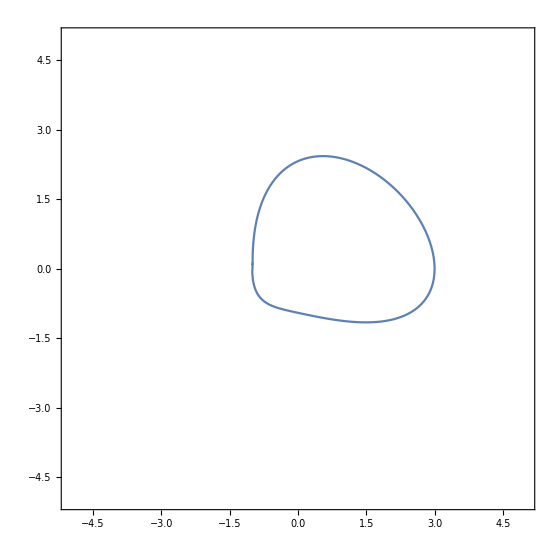

```mathematica
ContourPlot[Qplotf==0,{Y1,-5,5},{Y2,-5,5},MaxRecursion->4]
```

```mathematica
Qplotf=Factor[Qplot][[4]]
```

-10079771058864-24557472625536 Y1-13409022739032 Y1^2+5475719009840 Y1^3+3018096881549 Y1^4-1222680969348 Y1^5+458547819318 Y1^6+4136665788 Y1^7-288491127579 Y1^8+58501274112 Y1^9+36452793528 Y1^10-19115009856 Y1^11+3275776080 Y1^12-13742465272128 Y2-28665167583312 Y1 Y2-5780883750624 Y1^2 Y2+13732998126252 Y1^3 Y2-1744140189864 Y1^4 Y2-6333662125008 Y1^5 Y2+273895195824 Y1^6 Y2+211689752940 Y1^7 Y2+103483585368 Y1^8 Y2+74039392008 Y1^9 Y2-73157004576 Y1^10 Y2+16835001120 Y1^11 Y2+6453274298184 Y2^2+8145398436336 Y1 Y2^2-6148762376850 Y1^2 Y2^2-13697570456856 Y1^3 Y2^2-7233947719380 Y1^4 Y2^2+5605010568 Y1^5 Y2^2+1538856088758 Y1^6 Y2^2+180393316704 Y1^7 Y2^2-135370290312 Y1^8 Y2^2-112272041952 Y1^9 Y2^2+47504264400 Y1^10 Y2^2+10381155869664 Y2^3+6724472619852 Y1 Y2^3-19818622485864 Y1^2 Y2^3-13435337938464 Y1^3 Y2^3+6718738953096 Y1^4 Y2^3+3568806892836 Y1^5 Y2^3-833841988416 Y1^6 Y2^3-548465086224 Y1^7 Y2^3-47996776800 Y1^8 Y2^3+89957083680 Y1^9 Y2^3-2918365828803 Y2^4-4754957778612 Y1 Y2^4+2060696458782 Y1^2 Y2^4+8656125494364 Y1^3 Y2^4+2894357843037 Y1^4 Y2^4-2664678159792 Y1^5 Y2^4-760702063824 Y1^6 Y2^4+164222634816 Y1^7 Y2^4+125002271520 Y1^8 Y2^4-2385892327392 Y2^5+3570338331648 Y1 Y2^5+8232913697040 Y1^2 Y2^5-657845855856 Y1^3 Y2^5-3743943678576 Y1^4 Y2^5-535893673680 Y1^5 Y2^5+413682912288 Y1^6 Y2^5+131867701920 Y1^7 Y2^5+718596318528 Y2^6+1073496543264 Y1 Y2^6-2115092588904 Y1^2 Y2^6-2989403476560 Y1^3 Y2^6+48824016840 Y1^4 Y2^6+529593912288 Y1^5 Y2^6+107365778640 Y1^6 Y2^6-433409424840 Y2^7-2147498073576 Y1 Y2^7-1429724918520 Y1^2 Y2^7+423859898088 Y1^3 Y2^7+444716897184 Y1^4 Y2^7+67343153760 Y1^5 Y2^7-241991882424 Y2^8-177376792464 Y1 Y2^8+423791313768 Y1^2 Y2^8+253643011200 Y1^3 Y2^8+32216084640 Y1^4 Y2^8+97419827520 Y2^9+195657208128 Y1 Y2^9+94511782368 Y1^2 Y2^9+11453931360 Y1^3 Y2^9+36208846800 Y2^10+20050206048 Y1 Y2^10+2914658640 Y1^2 Y2^10+1456856928 Y2^11+481839840 Y1 Y2^11+42515280 Y2^12

```mathematica
Quq1=Factor[Quq][[4]]
```

665065728 Y1^2+1528595712 Y1^3+1255874112 Y1^4+616044672 Y1^5+369290688 Y1^6+169705792 Y1^7+69038608 Y1^8+26440768 Y1^9+7427872 Y1^10+1628544 Y1^11+499280 Y1^12+1036882944 Y1^2 Y2+2517951744 Y1^3 Y2+2481221376 Y1^4 Y2+1557153792 Y1^5 Y2+1017950592 Y1^6 Y2+416561568 Y1^7 Y2+142337792 Y1^8 Y2+48961344 Y1^9 Y2+11909504 Y1^10 Y2+2565920 Y1^11 Y2+997598592 Y2^2+2376026784 Y1 Y2^2+2866398192 Y1^2 Y2^2+3289131792 Y1^3 Y2^2+3628327752 Y1^4 Y2^2+2171503968 Y1^5 Y2^2+1096118280 Y1^6 Y2^2+455597536 Y1^7 Y2^2+166748960 Y1^8 Y2^2+44980288 Y1^9 Y2^2+7240400 Y1^10 Y2^2+1056525120 Y2^3+2843224416 Y1 Y2^3+4167344016 Y1^2 Y2^3+3955068264 Y1^3 Y2^3+3713398208 Y1^4 Y2^3+1993658936 Y1^5 Y2^3+938038864 Y1^6 Y2^3+388065216 Y1^7 Y2^3+102942720 Y1^8 Y2^3+13710880 Y1^9 Y2^3+775912365 Y2^4+2368562472 Y1 Y2^4+4625333712 Y1^2 Y2^4+3577632768 Y1^3 Y2^4+2514382472 Y1^4 Y2^4+1460058288 Y1^5 Y2^4+654813944 Y1^6 Y2^4+165902656 Y1^7 Y2^4+19052320 Y1^8 Y2^4+1060851924 Y2^5+1752123096 Y1 Y2^5+2993732208 Y1^2 Y2^5+2428906400 Y1^3 Y2^5+1705273712 Y1^4 Y2^5+800790584 Y1^5 Y2^5+196983488 Y1^6 Y2^5+20098720 Y1^7 Y2^5+1053808974 Y2^6+1333988568 Y1 Y2^6+1843701408 Y1^2 Y2^6+1488903632 Y1^3 Y2^6+733184288 Y1^4 Y2^6+176526528 Y1^5 Y2^6+16364240 Y1^6 Y2^6+690242580 Y2^7+913049280 Y1 Y2^7+916900128 Y1^2 Y2^7+487940984 Y1^3 Y2^7+118973504 Y1^4 Y2^7+10264160 Y1^5 Y2^7+315521973 Y2^8+380451600 Y1 Y2^8+230689728 Y1^2 Y2^8+58639360 Y1^3 Y2^8+4910240 Y1^4 Y2^8+81236304 Y2^9+68644152 Y1 Y2^9+19850688 Y1^2 Y2^9+1745760 Y1^3 Y2^9+9281736 Y2^10+4002048 Y1 Y2^10+444240 Y1^2 Y2^10+304128 Y2^11+73440 Y1 Y2^11+6480 Y2^12-7980788736 Y3-22333542912 Y1 Y3-26332573824 Y1^2 Y3-20901125952 Y1^3 Y3-16020278784 Y1^4 Y3-10057846560 Y1^5 Y3-4945480576 Y1^6 Y3-2162607296 Y1^7 Y3-806099712 Y1^8 Y3-232770464 Y1^9 Y3-63478272 Y1^10 Y3-13625920 Y1^11 Y3-12442595328 Y2 Y3-36436718592 Y1 Y2 Y3-50859565632 Y1^2 Y2 Y3-48005833248 Y1^3 Y2 Y3-40036621536 Y1^4 Y2 Y3-24201233424 Y1^5 Y2 Y3-10985689392 Y1^6 Y2 Y3-4456595408 Y1^7 Y2 Y3-1538454992 Y1^8 Y2 Y3-398934528 Y1^9 Y2 Y3-69179360 Y1^10 Y2 Y3-13797781056 Y2^2 Y3-43052354712 Y1 Y2^2 Y3-73969411680 Y1^2 Y2^2 Y3-69267376296 Y1^3 Y2^2 Y3-49334745264 Y1^4 Y2^2 Y3-27677853088 Y1^5 Y2^2 Y3-13003761008 Y1^6 Y2^2 Y3-4916924912 Y1^7 Y2^2 Y3-1287832816 Y1^8 Y2^2 Y3-186276960 Y1^9 Y2^2 Y3-19542250080 Y2^3 Y3-46638009612 Y1 Y2^3 Y3-75686534508 Y1^2 Y2^3 Y3-66559372256 Y1^3 Y2^3 Y3-45134134616 Y1^4 Y2^3 Y3-24879172016 Y1^5 Y2^3 Y3-10158385760 Y1^6 Y2^3 Y3-2605712960 Y1^7 Y2^3 Y3-330774560 Y1^8 Y2^3 Y3-24888498372 Y2^4 Y3-43956899856 Y1 Y2^4 Y3-60036522396 Y1^2 Y2^4 Y3-51668224504 Y1^3 Y2^4 Y3-33398523088 Y1^4 Y2^4 Y3-14657128928 Y1^5 Y2^4 Y3-3686963104 Y1^6 Y2^4 Y3-422617600 Y1^7 Y2^4 Y3-22298979240 Y2^5 Y3-34993538568 Y1 Y2^5 Y3-42097370124 Y1^2 Y2^5 Y3-32168957280 Y1^3 Y2^5 Y3-15121603352 Y1^4 Y2^5 Y3-3798925312 Y1^5 Y2^5 Y3-401795040 Y1^6 Y2^5 Y3-15010245216 Y2^6 Y3-22697144136 Y1 Y2^6 Y3-21390068580 Y1^2 Y2^6 Y3-11157758496 Y1^3 Y2^6 Y3-2879815184 Y1^4 Y2^6 Y3-287424160 Y1^5 Y2^6 Y3-7141585104 Y2^7 Y3-9226404684 Y1 Y2^7 Y3-5696122152 Y1^2 Y2^7 Y3-1576585408 Y1^3 Y2^7 Y3-153574880 Y1^4 Y2^7 Y3-1989738972 Y2^8 Y3-1814506992 Y1 Y2^8 Y3-589792800 Y1^2 Y2^8 Y3-59940480 Y1^3 Y2^8 Y3-266475096 Y2^9 Y3-133457472 Y1 Y2^9 Y3-16336800 Y1^2 Y2^9 Y3-12808368 Y2^10 Y3-2838240 Y1 Y2^10 Y3-246240 Y2^11 Y3+31071714048 Y3^2+97980565248 Y1 Y3^2+151843880016 Y1^2 Y3^2+146177158176 Y1^3 Y3^2+103631110320 Y1^4 Y3^2+58663106032 Y1^5 Y3^2+28053002920 Y1^6 Y3^2+10970333600 Y1^7 Y3^2+3542883200 Y1^8 Y3^2+995202768 Y1^9 Y3^2+173587800 Y1^10 Y3^2+81058330368 Y2 Y3^2+231716671488 Y1 Y2 Y3^2+361407298608 Y1^2 Y2 Y3^2+342359920080 Y1^3 Y2 Y3^2+235860820464 Y1^4 Y2 Y3^2+129348049832 Y1^5 Y2 Y3^2+59228397504 Y1^6 Y2 Y3^2+21419391584 Y1^7 Y2 Y3^2+5626681600 Y1^8 Y2 Y3^2+857714440 Y1^9 Y2 Y3^2+147866886072 Y2^2 Y3^2+346534103016 Y1 Y2^2 Y3^2+488876743782 Y1^2 Y2^2 Y3^2+436349333292 Y1^3 Y2^2 Y3^2+295534009102 Y1^4 Y2^2 Y3^2+156578946632 Y1^5 Y2^2 Y3^2+61309450768 Y1^6 Y2^2 Y3^2+15966994368 Y1^7 Y2^2 Y3^2+2177064680 Y1^8 Y2^2 Y3^2+194518178532 Y2^3 Y3^2+382689309084 Y1 Y2^3 Y3^2+491724879716 Y1^2 Y2^3 Y3^2+421765729308 Y1^3 Y2^3 Y3^2+260361576924 Y1^4 Y2^3 Y3^2+109823236928 Y1^5 Y2^3 Y3^2+28436519920 Y1^6 Y2^3 Y3^2+3572199280 Y1^7 Y2^3 Y3^2+190701525366 Y2^4 Y3^2+342650304552 Y1 Y2^4 Y3^2+394156968488 Y1^2 Y2^4 Y3^2+289519292436 Y1^3 Y2^4 Y3^2+133264062014 Y1^4 Y2^4 Y3^2+34873298704 Y1^5 Y2^4 Y3^2+4124076760 Y1^6 Y2^4 Y3^2+141214502160 Y2^5 Y3^2+233016344760 Y1 Y2^5 Y3^2+214473592412 Y1^2 Y2^5 Y3^2+111487639172 Y1^3 Y2^5 Y3^2+30393931584 Y1^4 Y2^5 Y3^2+3454552760 Y1^5 Y2^5 Y3^2+72347665140 Y2^6 Y3^2+99105497856 Y1 Y2^6 Y3^2+62832380458 Y1^2 Y2^6 Y3^2+18722263840 Y1^3 Y2^6 Y3^2+2107760920 Y1^4 Y2^6 Y3^2+22180797036 Y2^7 Y3^2+21726195204 Y1 Y2^7 Y3^2+7792659264 Y1^2 Y2^7 Y3^2+919713840 Y1^3 Y2^7 Y3^2+3467586438 Y2^8 Y3^2+1962259920 Y1 Y2^8 Y3^2+274503240 Y1^2 Y2^8 Y3^2+219603312 Y2^9 Y3^2+50966280 Y1 Y2^9 Y3^2+4558680 Y2^10 Y3^2-138702652992 Y3^3-397024449696 Y1 Y3^3-580016264544 Y1^2 Y3^3-539945278392 Y1^3 Y3^3-374492747280 Y1^4 Y3^3-205384590448 Y1^5 Y3^3-89805500176 Y1^6 Y3^3-31950217576 Y1^7 Y3^3-8874774016 Y1^8 Y3^3-1363828880 Y1^9 Y3^3-422684977536 Y2 Y3^3-1038398548608 Y1 Y2 Y3^3-1418445338544 Y1^2 Y2 Y3^3-1275509948460 Y1^3 Y2 Y3^3-857135448260 Y1^4 Y2 Y3^3-443188856404 Y1^5 Y2 Y3^3-170750217300 Y1^6 Y2 Y3^3-45416473296 Y1^7 Y2 Y3^3-6451211880 Y1^8 Y2 Y3^3-726303135456 Y2^2 Y3^3-1567010740932 Y1 Y2^2 Y3^3-1994179123440 Y1^2 Y2^2 Y3^3-1696008327512 Y1^3 Y2^2 Y3^3-1020600131520 Y1^4 Y2^2 Y3^3-425483706904 Y1^5 Y2^2 Y3^3-113565067876 Y1^6 Y2^2 Y3^3-15207433040 Y1^7 Y2^2 Y3^3-870746660016 Y2^3 Y3^3-1717448534508 Y1 Y2^3 Y3^3-1950464512568 Y1^2 Y2^3 Y3^3-1403554692448 Y1^3 Y2^3 Y3^3-643481508492 Y1^4 Y2^3 Y3^3-175600712260 Y1^5 Y2^3 Y3^3-22642585760 Y1^6 Y2^3 Y3^3-746456000136 Y2^4 Y3^3-1314056965848 Y1 Y2^4 Y3^3-1206574223040 Y1^2 Y2^4 Y3^3-633523638240 Y1^3 Y2^4 Y3^3-182193014160 Y1^4 Y2^4 Y3^3-23093063280 Y1^5 Y2^4 Y3^3-427657729884 Y2^5 Y3^3-617603268576 Y1 Y2^5 Y3^3-404536995672 Y1^2 Y2^5 Y3^3-129073698628 Y1^3 Y2^5 Y3^3-16536930440 Y1^4 Y2^5 Y3^3-147626513292 Y2^6 Y3^3-154650617892 Y1 Y2^6 Y3^3-60520428528 Y1^2 Y2^6 Y3^3-8249435040 Y1^3 Y2^6 Y3^3-27013362732 Y2^7 Y3^3-17001893268 Y1 Y2^7 Y3^3-2752823520 Y1^2 Y2^7 Y3^3-2151790380 Y2^8 Y3^3-558355680 Y1 Y2^8 Y3^3-53009640 Y2^9 Y3^3+424280821392 Y3^4+1117966454784 Y1 Y3^4+1557593242632 Y1^2 Y3^4+1425494757096 Y1^3 Y3^4+946915566821 Y1^4 Y3^4+477236089412 Y1^5 Y3^4+185295910998 Y1^6 Y3^4+51334013916 Y1^7 Y3^4+7349319365 Y1^8 Y3^4+1340048863152 Y2 Y3^4+3137785145280 Y1 Y2 Y3^4+4034056471740 Y1^2 Y2 Y3^4+3422210635028 Y1^3 Y2 Y3^4+2042812128092 Y1^4 Y2 Y3^4+856978668280 Y1^5 Y2 Y3^4+235689340640 Y1^6 Y2 Y3^4+32674938380 Y1^7 Y2 Y3^4+2247420405942 Y2^2 Y3^4+4764495075972 Y1 Y2^2 Y3^4+5430280482146 Y1^2 Y2^2 Y3^4+3894182988460 Y1^3 Y2^2 Y3^4+1806495816424 Y1^4 Y2^2 Y3^4+513264466820 Y1^5 Y2^2 Y3^4+70224336570 Y1^6 Y2^2 Y3^4+2395274172432 Y2^3 Y3^4+4454138977368 Y1 Y2^3 Y3^4+4139144815700 Y1^2 Y2^3 Y3^4+2219705069716 Y1^3 Y2^3 Y3^4+672574963120 Y1^4 Y2^3 Y3^4+92703619400 Y1^5 Y2^3 Y3^4+1612705005477 Y2^4 Y3^4+2449694673036 Y1 Y2^4 Y3^4+1666998242532 Y1^2 Y2^4 Y3^4+567725237980 Y1^3 Y2^4 Y3^4+81030440375 Y1^4 Y2^4 Y3^4+646483950072 Y2^5 Y3^4+722251827828 Y1 Y2^5 Y3^4+306426381528 Y1^2 Y2^5 Y3^4+47531217720 Y1^3 Y2^5 Y3^4+139986374904 Y2^6 Y3^4+97109789040 Y1 Y2^6 Y3^4+18149644890 Y1^2 Y2^6 Y3^4+13792718880 Y2^7 Y3^4+4113535860 Y1 Y2^7 Y3^4+425211525 Y2^8 Y3^4-996817288896 Y3^5-2526979140936 Y1 Y3^5-3317430850656 Y1^2 Y3^5-2813791028412 Y1^3 Y3^5-1680187588244 Y1^4 Y3^5-720041580532 Y1^5 Y3^5-204545171484 Y1^6 Y3^5-28563197400 Y1^7 Y3^5-3117535812000 Y2 Y3^5-7038148289892 Y1 Y2 Y3^5-8156595164796 Y1^2 Y2 Y3^5-5919801852136 Y1^3 Y2 Y3^5-2811075156844 Y1^4 Y2 Y3^5-827499735504 Y1^5 Y2 Y3^5-116859685420 Y1^6 Y2 Y3^5-4674584174856 Y2^2 Y3^5-9153919204812 Y1 Y2^2 Y3^5-8714828083068 Y1^2 Y2^2 Y3^5-4819963407536 Y1^3 Y2^2 Y3^5-1532463355208 Y1^4 Y2^2 Y3^5-223633368500 Y1^5 Y2^2 Y3^5-3976319541732 Y2^3 Y3^5-6356379458424 Y1 Y2^3 Y3^5-4518542105932 Y1^2 Y2^3 Y3^5-1636749531400 Y1^3 Y2^3 Y3^5-253802567080 Y1^4 Y2^3 Y3^5-1933477768944 Y2^4 Y3^5-2301692312784 Y1 Y2^4 Y3^5-1053935562036 Y1^2 Y2^4 Y3^5-182125202820 Y1^3 Y2^4 Y3^5-506199902400 Y2^5 Y3^5-384891153876 Y1 Y2^5 Y3^5-81900395640 Y1^2 Y2^5 Y3^5-61783480296 Y2^6 Y3^5-21253663980 Y1 Y2^6 Y3^5-2452166460 Y2^7 Y3^5+1834592807736 Y3^6+4392596510424 Y1 Y3^6+5224040676278 Y1^2 Y3^6+3881075016104 Y1^3 Y3^6+1900592882874 Y1^4 Y3^6+575852404012 Y1^5 Y3^6+81916209820 Y1^6 Y3^6+5159426655348 Y2 Y3^6+10656585614964 Y1 Y2 Y3^6+10509198398536 Y1^2 Y2 Y3^6+6034474969392 Y1^3 Y2 Y3^6+1997085841568 Y1^4 Y2 Y3^6+300592650060 Y1^5 Y2 Y3^6+6274593578916 Y2^2 Y3^6+10589061378204 Y1 Y2^2 Y3^6+7901053092336 Y1^2 Y2^2 Y3^6+3024607375976 Y1^3 Y2^2 Y3^6+496396730710 Y1^4 Y2^2 Y3^6+3957942447480 Y2^3 Y3^6+5023994319612 Y1 Y2^3 Y3^6+2469261025680 Y1^2 Y2^3 Y3^6+463722956160 Y1^3 Y2^3 Y3^6+1299244686822 Y2^4 Y3^6+1077320940084 Y1 Y2^4 Y3^6+255585017250 Y1^2 Y2^4 Y3^6+199444836816 Y2^5 Y3^6+78207731280 Y1 Y2^5 Y3^6+10334930130 Y2^6 Y3^6-2502470395680 Y3^7-5476040321004 Y1 Y3^7-5642347703000 Y1^2 Y3^7-3369158929440 Y1^3 Y3^7-1147673616908 Y1^4 Y3^7-174220219400 Y1^5 Y3^7-5822090028480 Y2 Y3^7-10419830529396 Y1 Y2 Y3^7-8177454394284 Y1^2 Y2 Y3^7-3274291948400 Y1^3 Y2 Y3^7-554830748140 Y1^4 Y2 Y3^7-5368504363236 Y2^2 Y3^7-7269126247944 Y1 Y2^2 Y3^7-3802442291988 Y1^2 Y2^2 Y3^7-756576338280 Y1^3 Y2^2 Y3^7-2347452984888 Y2^3 Y3^7-2107691586900 Y1 Y2^3 Y3^7-544039602480 Y1^2 Y2^3 Y3^7-466705784124 Y2^4 Y3^7-204350007060 Y1 Y2^4 Y3^7-31874679360 Y2^5 Y3^7+2451425006805 Y3^8+4666280381364 Y1 Y3^8+3840214590986 Y1^2 Y3^8+1586886341396 Y1^3 Y3^8+271903574030 Y1^4 Y3^8+4400130436380 Y2 Y3^8+6340683518520 Y1 Y2 Y3^8+3487696274976 Y1^2 Y2 Y3^8+718199475780 Y1^3 Y2 Y3^8+2866745681208 Y2^2 Y3^8+2758090581396 Y1 Y2^2 Y3^8+755771442390 Y1^2 Y2^2 Y3^8+777433924080 Y2^3 Y3^8+371005905960 Y1 Y2^3 Y3^8+71124614055 Y2^4 Y3^8-1666973626116 Y3^9-2539310775588 Y1 Y3^9-1447847557716 Y1^2 Y3^9-302648748840 Y1^3 Y3^9-2138698325700 Y2 Y3^9-2175372261360 Y1 Y2 Y3^9-618988705380 Y1^2 Y2 Y3^9-877240650960 Y2^2 Y3^9-445534367220 Y1 Y2^2 Y3^9-111766861800 Y2^3 Y3^9+738561137670 Y3^10+782698906260 Y1 Y3^10+227180914020 Y1^2 Y3^10+601768504800 Y2 Y3^10+318586103100 Y1 Y2 Y3^10+117338969250 Y2^2 Y3^10-189411898500 Y3^11-102835737000 Y1 Y3^11-73913917500 Y2 Y3^11+21141253125 Y3^12

```mathematica
ContourPlot3D[Quq1,{Y1,-5,5},{Y2,0,10},{Y3,0,1},MaxRecursion->4]
```

-Graphics3D-